```mathematica
FullSimplify[Integrate[ⅇ^(-ⅈ k x) ,{x,-d-w/2,-d+w/2}]+Integrate[ⅇ^(-ⅈ k x) ,{x,d-w/2,d+w/2}]]
```

(4 Cos[d k] Sin[(k w)/2])/k

```mathematica
Integrate[ⅇ^(ⅈ (k)^2 t+ⅈ k x) Cos[d k] Sinc[(k w)/2],{k,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(ⅈ k^2 t+ⅈ k x) Cos[d k] Sinc[(k w)/2]ⅆk

```mathematica
VelocityField3[x_, t_, d_ ]:=-(√(2/π) Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))
```

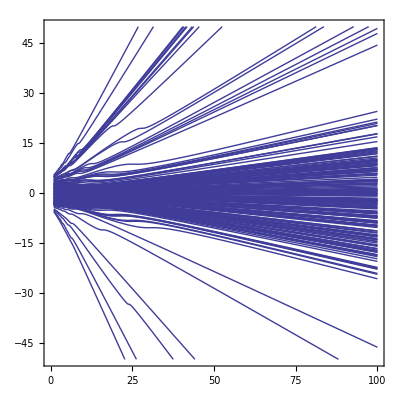

```mathematica
ddd = 9.0;
www=1.0;
kkk = 1.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-VelocityField3[y[t], t, ddd ]2,y[0.1]== RandomVariate[UniformDistribution[{-ddd,ddd}]]},y,{t,1,100}],{200}];
Plot[{(y[t]/2)/.HollandtablU},{t,1,100}, PlotRange->{{0,100},{-50,50}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20}]
```

```mathematica
VelocityField5[x_,t_,d_,w_]:=-(√(2/π) ((Cos[(-2 d+w-2 x)^2/(16 t)]+Cos[(2 d+w-2 x)^2/(16 t)]-Cos[(d+w/2+x)^2/(4 t)]-Cos[(-2 d+w+2 x)^2/(16 t)]) (FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])-(FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)]) (Sin[(-2 d+w-2 x)^2/(16 t)]+Sin[(2 d+w-2 x)^2/(16 t)]-Sin[(d+w/2+x)^2/(4 t)]-Sin[(-2 d+w+2 x)^2/(16 t)])))/(√t ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2))
```

```mathematica
N[100/16]
```

6.25

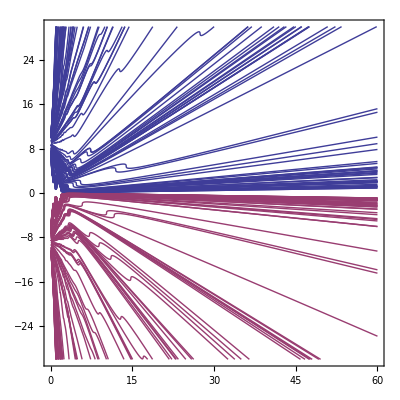

```mathematica
ddd = 9.0;
σσσ=2.0;
Parallelize[
HollandtablU=Table[NDSolve[{D[y[t], t]==-VelocityField5[y[t], t, ddd,σσσ ],y[0.1]== ddd+RandomVariate[UniformDistribution[{-σσσ-1,σσσ}]]},y,{t,0.1,60}],{7*16}];
HollandtablD=
Table[NDSolve[{D[y[t], t]==-VelocityField5[y[t], t, ddd,σσσ ],y[0.1]== -ddd+RandomVariate[UniformDistribution[{-σσσ,σσσ+1}]]},y,{t,0.1,60}],{7*16}];
];
Plot[{y[t]/.HollandtablU,y[t]/.HollandtablD},{t,0.1,60}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20}]
```

```mathematica
Plot[{y[t]/.HollandtablU,y[t]/.HollandtablD},{t,0.1,60}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->26}]
```

-Graphics-

```mathematica
Integrate[(√t ((FresnelC[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelC[(d+w/2-x)/(√(2 π) √t)]+FresnelC[(-d+w/2+x)/(√(2 π) √t)]+FresnelC[(d+w/2+x)/(√(2 π) √t)])^2+(FresnelS[(-2 d+w-2 x)/(2 √(2 π) √t)]+FresnelS[(d+w/2-x)/(√(2 π) √t)]+FresnelS[(-d+w/2+x)/(√(2 π) √t)]+FresnelS[(d+w/2+x)/(√(2 π) √t)])^2)),{x,-∞,∞}]
```

$Aborted